```mathematica
data=Import["/home/freek/Documents/temp2/Introgression/Rfiles/data/loggrowthA.csv"]//Flatten;
```

```mathematica
data=Table[{t,data[[t+1]]},{t,0,19}];
```

```mathematica
nA[nA0_,WA_,t_]:=nA0 WA^t
```

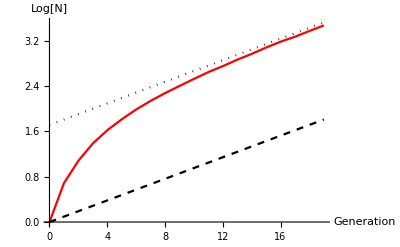

```mathematica
out=Show[
{ListLinePlot[Table[{t,Log[nA[1/0.18,1.1,t]]},{t,0,19}],AxesLabel->{"Generation","Log[N]"},PlotStyle->{Black,Dotted},PlotRange->{Automatic,{0,Automatic}}],ListLinePlot[data,PlotStyle->Red],

ListLinePlot[Table[{t,Log[nA[1,1.1,t]]},{t,0,19}],PlotStyle->{Black,Dashed}]
}
]
```

```mathematica
Export["/home/freek/Documents/temp2/Introgression/Rfiles/figures/PlotSimGrowth.eps",out]
```

/home/freek/Documents/temp2/Introgression/Rfiles/figures/PlotSimGrowth.eps

```mathematica
Clear[nA]
```

```mathematica
RSolve[{p[t+1]==p[t] WA/(p[t]WA+(1-p[t])Wa),p[0]==nA0/(nA0+na0)},p[t],t]//FullSimplify
```

{{p[t]→nA0/(nA0+na0 (Wa/WA)^t)}}

```mathematica
Reduce[D[pA0/(pA0+(1-pA0) (Wa/WA)^t),pA0 ]<0]
```

(pA0≤0&&(Wa/WA)^t<0)||(0<pA0<1&&((Wa/WA)^t<pA0/(-1+pA0)||pA0/(-1+pA0)<(Wa/WA)^t<0))||(pA0≥1&&(Wa/WA)^t<0)

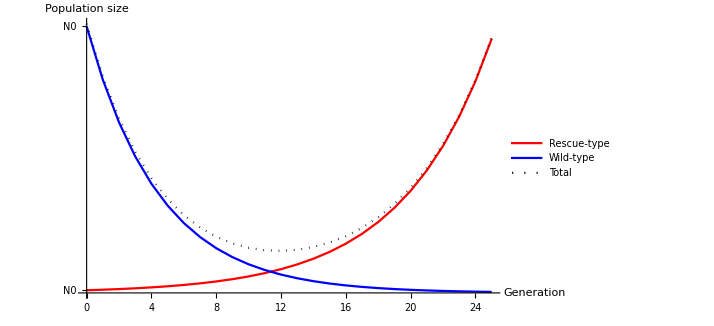

```mathematica
grow=Table[{t,nA[1,1.2,t]},{t,0,25}];
shring=Table[{t,nA[100,0.8,t]},{t,0,25}];
total=grow[[;;,2]]+shring[[;;,2]];
total=Table[{t,total[[t+1]]},{t,0,25}];
plot=Legended[
ListLinePlot[{grow,shring,total},PlotStyle->{Red,Blue,{Black,Dotted}},Ticks->{{}, {{100,"N0"},{1,"N0"}}},AxesLabel->{"Generation","Population size"}],
Placed[
LineLegend[{
{Red},{Blue},{Black,Dotted},NULL
},
{
Style["Rescue-type"],
Style["Wild-type"],
Style["Total"]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{.5,0.5}
] 
]
```

```mathematica
Export["/home/freek/Documents/temp2/Introgression/Rfiles/figures/WhatisRescue.eps",plot]
```

/home/freek/Documents/temp2/Introgression/Rfiles/figures/WhatisRescue.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["/home/freek/Documents/temp2/Introgression/Rfiles/figures/WhatisRescue.eps"]]]
```

```mathematica
data=Import["/home/freek/Documents/temp2/Introgression/Rfiles/data/fixationsimulations.csv"];
```

```mathematica
data
```

{{1,0.0464943},{2,0.0878272},{3,0.137665},{4,0.184809},{5,0.22119},{6,0.261849},{7,0.297442},{8,0.320821},{9,0.354736},{10,0.389105},{11,0.406339},{12,0.458716},{13,0.457666},{14,0.484731},{15,0.526039},{16,0.540833},{17,0.56243},{18,0.588235},{19,0.62422},{20,0.609756}}

```mathematica
Fix[k_,s_]:=2 k s;
```

{{1,0.2},{2,0.4},{3,0.6},{4,0.8},{5,1.}}

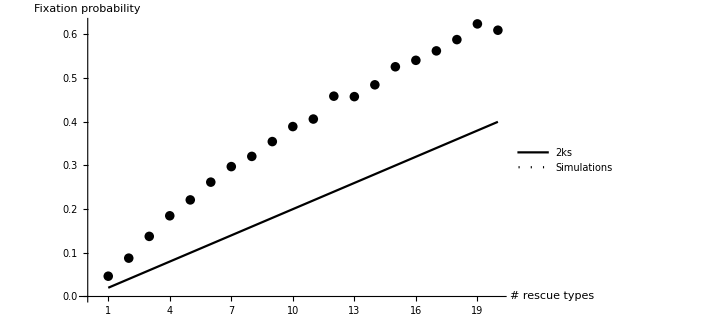

```mathematica
Legended[Show[
{ListPlot[data,AxesLabel->{"# rescue types","Fixation probability"},Ticks->{Table[i,{i,1,20}], Automatic},PlotStyle->{Black,Dashed}],
ListLinePlot[Table[{i,Fix[i,.01]},{i,1,20}],PlotStyle->Black]
}
],
Placed[
LineLegend[{
{Black},{Black,Dotted},NULL
},
{
Style["2ks"],
Style["Simulations"]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{.8,0.2}
] 

]
```